## Installations

### Initializations

```mathematica
Clear["Global`*"]
Needs["SymbolicC`"];
targetDir=NotebookDirectory[];
SetDirectory[targetDir];
```

### Install Packages: Nbody.

```mathematica
MyPackageDirectory=ToFileName[{ParentDirectory[ParentDirectory[]],"Packages"}]
```

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/4-Artikulurako-I/C-inplementazioa/Packages/

```mathematica
Get["NBodyProblem`",Path->MyPackageDirectory];
Get["MyFunctions`",Path->MyPackageDirectory];
```

### Plot Style

```mathematica
StyleQuad=Red;
StyleIdeal=Black;
StyleMachine=Lighter[Blue,.6];
StyleClassic=Lighter[Gray,.6];
StyleError=Black;
StyleEstimation=Lighter[Blue,.6];
MarkerQuad="○"; (*○  △    □*)
MarkerIdeal="▲"; (*●  ▲  ■*)
MarkerMachine="■";
```

## Filenames

```mathematica
DataDirectory="Data/";
ImagesDirectory="Images/";
```

```mathematica
filey0=NotebookDirectory[]<>DataDirectory<>"Datay0.bin";
fileA=NotebookDirectory[]<>DataDirectory<>"outA.bin";
fileB=NotebookDirectory[]<>DataDirectory<>"outB.bin";
fileC=NotebookDirectory[]<>DataDirectory<>"outC.bin";
```

## Parameters (N9-Body Problem)

### Problem parameters and initial values.

```mathematica
prec=100;
n=10;
neq=60;
```

```mathematica
(*SetPrecision[{q,v},Infinity]*)
q={-7136455862775249*10^(-18),-2647034369220534*10^(-18),-9229892504941378*10^(-19),-1372300611745480*10^(-16),-4032407527793943*10^(-16),-2014122987317287*10^(-16),-7254387522691935*10^(-16),-4892128029339700*10^(-17),2371764891109850*10^(-17),-1842952394356757*10^(-16),8847598253974531*10^(-16),3838137276110072*10^(-16),1383579465953266*10^(-15),-1245818066351708*10^(-18),-3788315564915632*10^(-17),3994040700303292*10^(-15),2733931723325132*10^(-15),1074589265949394*10^(-15),6399272408763718*10^(-15),6172010767717908*10^(-15),2273847765456232*10^(-15),1442471996208113*10^(-14),-1250891689477710*10^(-14),-5682610766007904*10^(-15),1680491056380734*10^(-14),-2298274829624356*10^(-14),-9825345996234370*10^(-15),-9882509358849774*10^(-15),-2798158407992709*10^(-14),-5754636675692544*10^(-15)};

v={5378460509592847*(10^-21),-6758188009917985*(10^-21),-3032853127305018*(10^-21),2137177408741818*(10^-17),-4933057744882007*(10^-18),-4850466138071373*(10^-18),803495961125404*(10^-18),-1849859567968007*(10^-17),-8372768171238536*(10^-18),-1719773059676588*(10^-17),-2909600195799265*(10^-18),-1261542476876303*(10^-18),6768779911283246*(10^-19),1380727932950537*(10^-17),6314867575256010*(10^-18),-4562935075888487*(10^-18),5874703960836767*(10^-18),2629270063133951*(10^-18),-4286973412228722*(10^-18),3521586381737719*(10^-18),1638898660518162*(10^-18),2683483741090174*(10^-18),2455245617100571*(10^-18),1037376262575060*(10^-18),2584652364125945*(10^-18),1661666963130189*(10^-18),6157833197233258*(10^-19),3034132360796665*(10^-18),-1134370373622282*(10^-18),-1268166831777267*(10^-18)};
```

```mathematica
u=Flatten[{q,v}];
```

```mathematica
Gm={2959122083039253*(10^-19),4912547451939157*(10^-26),7243452327305554*(10^-25),8997011596502244*(10^-25),9549548697395966*(10^-26),2825345791109909*(10^-22),8459705996177680*(10^-23),1292024916910406*(10^-23),1524357330444817*(10^-23),2166807318808926*(10^-26)};(*sun,Mercury,Venus,,Earth+Moon,Mars,Jupiter,Saturn,Uranus,Neptune,Pluto*)
```

```mathematica
preal=parameters=Gm;
pint={0,0};
```

```mathematica
u0=Chdata[u,preal];
u0D=N[u0];
u0DD=SetPrecision[u0D,prec];
ee0 =u0 - u0DD;
```

```mathematica
stru0=ExportString[u0,"Real128"];
stre0 = ExportString[u0*0.0,"Real128"];
strrpar = ExportString[preal, "Real128"];
```

```mathematica
N[ee0,20];
```

### Integration parameters.

```mathematica
t0=0.;tend=1000000.;(*10000.*)
tend=1000.;
h=2.;
sampling=100;
```

```mathematica
codfun0=2; (*NBody Problem*)
codfunX=12; (*NBody ProblemX*)
approx = 1; 
ns= 6;
nstep=(tend-t0)/h;
nout=nstep/sampling
```

5.

### RKG parameters

```mathematica
neq=60;
prec=100;
HAM=NBodyHam2;
```

## Analisis-I

### Import and mean

```mathematica
noutA=Round[nout]+1;
nstat=10; 
dd1= (2neq+1)
dd2= (3neq+1);
```

121

```mathematica
outA=SetPrecision[ArrayReshape[BinaryReadList[fileA,"Real128"],{nstat,noutA,dd1}],prec];
outB=SetPrecision[ArrayReshape[BinaryReadList[fileB,"Real128"],{nstat,noutA,dd1}],prec];
outC=SetPrecision[ArrayReshape[BinaryReadList[fileC,"Real64"],{nstat,noutA,dd2}],prec];
tpA=Flatten[Take[outA[[1]],All,{1,1}]];
tpB=Flatten[Take[outB[[1]],All,{1,1}]];
tpC=Flatten[Take[outC[[1]],All,{1,1}]];
```

```mathematica
Length[outA[[1]]]
```

6

```mathematica
{Length[outA],Length[outA[[1]]]}
```

{10,6}

```mathematica
{Length[outB],Length[outB[[1]]]}
```

{10,6}

```mathematica
{Length[outC],Length[outC[[1]]]}
```

{10,6}

```mathematica
{MeanHamA,MeanErrA,EndHamA}=FunMeanHerr[outA,outA,nstat,noutA,HAM, parameters,neq,prec] ;
```

```mathematica
{MeanHamB,MeanErrB,EndHamB}=FunMeanHerr[outB,outA, nstat,noutA,HAM, parameters,neq,prec] ;
```

```mathematica
{MeanHamC,MeanErrC, EndHamC}=FunMeanHerr[outC,outA, nstat,noutA,HAM, parameters,neq,prec] ;
```

```mathematica
step=4;
HamerrA=FunHerr[outA,nstat,noutA,HAM, parameters,neq,prec,step] ;
```

```mathematica
HamerrB=FunHerr[outB,nstat,noutA,HAM, parameters,neq,prec,step] ;
```

```mathematica
HamerrC=FunHerr[outC,nstat,noutA,HAM, parameters,neq,prec,step] ;
```

### Graphics-I (Energy)

```mathematica
MeanHamAdata = Transpose[{tpA,MeanHamA}];
MeanHamBdata = Transpose[{tpB,MeanHamB}];
MeanHamCdata = Transpose[{tpC,MeanHamC}];
```

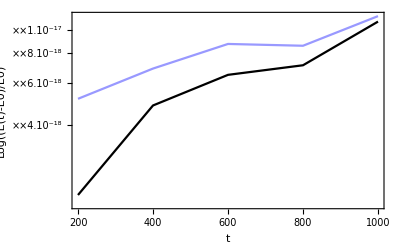

```mathematica
plot=ListLogPlot[{MeanHamBdata,MeanHamCdata},AxesLabel->{"t","Log((E(t)-E0)/E0)"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Log((E(t)-E0)/E0)"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot6a.pdf",Show[plot] ];
```

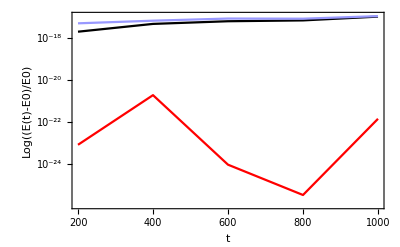

```mathematica
plot=ListLogPlot[{MeanHamAdata,MeanHamBdata,MeanHamCdata},AxesLabel->{"t","Log((E(t)-E0)/E0)"},Joined->True,
(*PlotRange->All,*)
(*PlotLegends->Placed[{"Quadruple","ideal","mean (rdigits-0)"(*,"standard deviation"*)},Below],*)
PlotTheme->"Detailed",
PlotStyle->{StyleQuad,StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Log((E(t)-E0)/E0)"}]
```

### Graphics-II (Global Error)

```mathematica
MeanErrAdata = Transpose[{tpA,MeanErrA}];
MeanErrBdata = Transpose[{tpB,MeanErrB}];
MeanErrCdata = Transpose[{tpC,MeanErrC}];
```

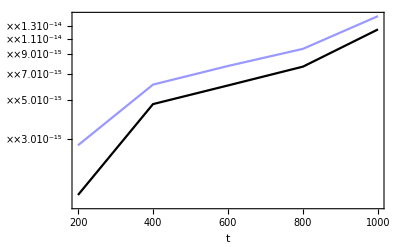

```mathematica
plot=ListLogPlot[{Drop[MeanErrBdata,1],Drop[MeanErrCdata,1]},AxesLabel->{"t","Pos.Error"},Joined->True,PlotRange->All,
(*PlotLegends->Placed[{"ideal","rdigits=0"(*,"rdigits=3"*)},Below],*)
(*PlotRange->All,*)
PlotTheme->"Detailed",
PlotStyle->{StyleIdeal,StyleMachine},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot6b.pdf",Show[plot] ];
```

### Graphics-III (Histogram)

#### Ideal

```mathematica
Hamerdif=HamerrB 10^15;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/4},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[NotebookDirectory[]<>ImagesDirectory<>"brouwer4e.pdf",Show[ir1,ir2]]
```

Mean[{}]

StandardDeviation::shlen: The argument {} should have at least two elements.

StandardDeviation[{}]

Histogram::hbins: The bin specification {StandardDeviation[{}]/4} cannot be used to determine either how many or which bins to use.

Plot::plln: Limiting value -16 StandardDeviation[{}] in {x,-16 σ,16 σ} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{},{StandardDeviation[{}]/4},PDF],Plot[PDF[NormalDistribution[μ,σ],x],{x,-16 σ,16 σ},PlotStyle→{Red,Thick},PlotRange→All,WorkingPrecision→prec]].

Show[Histogram[{},{StandardDeviation[{}]/4},PDF],Plot[PDF[NormalDistribution[μ,σ],x],{x,-16 σ,16 σ},PlotStyle→{Red,Thick},PlotRange→All,WorkingPrecision→prec]]

Plot::plln: Limiting value -16 StandardDeviation[{}] in {x,-16 σ,16 σ} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{},{StandardDeviation[{}]/4},PDF],Plot[PDF[NormalDistribution[μ,σ],x],{x,-16 σ,16 σ},PlotStyle→{Red,Thick},PlotRange→All,WorkingPrecision→prec]].

Plot::plln: Limiting value -16 StandardDeviation[{}] in {x,-16 σ,16 σ} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{},{StandardDeviation[{}]/4},PDF],Plot[PDF[NormalDistribution[μ,σ],x],{x,-16 σ,16 σ},PlotStyle→{Red,Thick},PlotRange→All,WorkingPrecision→prec]].

Plot::plln: Limiting value -16 StandardDeviation[{}] in {x,-16 σ,16 σ} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{},{StandardDeviation[{}]/4},PDF],Plot[PDF[NormalDistribution[μ,σ],x],{x,-16 σ,16 σ},PlotStyle→{Red,Thick},PlotRange→All,WorkingPrecision→prec]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/4-Artikulurako-I/C-inplementazioa/Experiments/Nbody/Images/brouwer4e.pdf

#### Machine precision (rdigits=0)

```mathematica
Hamerdif=HamerrC 10^15;
μ=Mean[Hamerdif]
σ=StandardDeviation[Hamerdif]
ir1=Histogram[Hamerdif,{σ/4},"PDF"];
ir2=Plot[PDF[NormalDistribution[μ,σ],x],{x,-16*σ,16*σ},PlotStyle->{Red,Thick},PlotRange->All,WorkingPrecision->prec];
Show[ir1,ir2]
Export[NotebookDirectory[]<>ImagesDirectory<>"brouwer4f.pdf",Show[ir1,ir2]]
```

Mean[{}]

StandardDeviation::shlen: The argument {} should have at least two elements.

StandardDeviation[{}]

Histogram::hbins: The bin specification {StandardDeviation[{}]/4} cannot be used to determine either how many or which bins to use.

Plot::plln: Limiting value -16 StandardDeviation[{}] in {x,-16 σ,16 σ} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{},{StandardDeviation[{}]/4},PDF],Plot[PDF[NormalDistribution[μ,σ],x],{x,-16 σ,16 σ},PlotStyle→{Red,Thick},PlotRange→All,WorkingPrecision→prec]].

Show[Histogram[{},{StandardDeviation[{}]/4},PDF],Plot[PDF[NormalDistribution[μ,σ],x],{x,-16 σ,16 σ},PlotStyle→{Red,Thick},PlotRange→All,WorkingPrecision→prec]]

Plot::plln: Limiting value -16 StandardDeviation[{}] in {x,-16 σ,16 σ} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{},{StandardDeviation[{}]/4},PDF],Plot[PDF[NormalDistribution[μ,σ],x],{x,-16 σ,16 σ},PlotStyle→{Red,Thick},PlotRange→All,WorkingPrecision→prec]].

Plot::plln: Limiting value -16 StandardDeviation[{}] in {x,-16 σ,16 σ} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{},{StandardDeviation[{}]/4},PDF],Plot[PDF[NormalDistribution[μ,σ],x],{x,-16 σ,16 σ},PlotStyle→{Red,Thick},PlotRange→All,WorkingPrecision→prec]].

Plot::plln: Limiting value -16 StandardDeviation[{}] in {x,-16 σ,16 σ} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[{},{StandardDeviation[{}]/4},PDF],Plot[PDF[NormalDistribution[μ,σ],x],{x,-16 σ,16 σ},PlotStyle→{Red,Thick},PlotRange→All,WorkingPrecision→prec]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

/home/joseba/Mahaigaina/PIC/Softwatea/garapenak/4-Artikulurako-I/C-inplementazioa/Experiments/Nbody/Images/brouwer4f.pdf

### Tables

#### Quadruple

```mathematica
MeanD0=0.; (*(SD0A/nstat)/steps*100;*)
MaxDE=Max[MeanHamA]//N;
Hamerdif=Drop[MeanHamA ,1]-Drop[ MeanHamA,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrA]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,1.92558×10^-21,2.86199×10^-23,1.35987×10^-21,0.}

#### Ideal

```mathematica
MeanD0=0.;(*(SD0B/nstat)/steps*100;*)
MaxDE=Max[MeanHamB]//N;
Hamerdif=Drop[MeanHamB ,1]-Drop[ MeanHamB,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrB]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,1.0808×10^-17,2.1616×10^-18,1.15831×10^-18,1.24389×10^-14}

#### Machine

```mathematica
MeanD0=0.;(*(SD0C/nstat)/steps*100;*)
MaxDE=Max[MeanHamC]//N;
Hamerdif=Drop[MeanHamC ,1]-Drop[ MeanHamC,-1];
μ=Mean[Hamerdif]//N;
σ=StandardDeviation[Hamerdif]//N;
Gerror=Max[MeanErrC]//N;
{N[MeanD0],MaxDE,μ,σ,Gerror}
```

{0.,1.13898×10^-17,2.27797×10^-18,1.93643×10^-18,1.47809×10^-14}

## Analisis-II: error estimation

### Estimation

```mathematica
MeanErrCdata = Transpose[{tpC,MeanErrC}];
```

```mathematica
{MeanEstC,DesvEstC,MeanQtyC,DesvQtyC}=FunMeanEst[outC,outA,nstat,noutA,neq,prec];
```

```mathematica
MeanEstCdata = Transpose[{tpC,MeanEstC}];
DesvdataC1=Transpose[{tpC,MeanEstC+DesvEstC}];
DesvdataC2=Transpose[{tpC,MeanEstC-DesvEstC}];
```

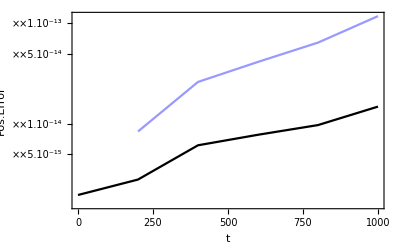

```mathematica
plot=ListLogPlot[{Abs[MeanErrCdata],Abs[MeanEstCdata]},AxesLabel->{"t","Pos.Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
PlotTheme->"Detailed",
PlotStyle->{StyleError,StyleEstimation},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot7a.pdf",Show[plot]];
```

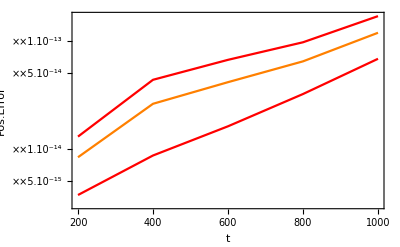

```mathematica
plot6b=ListLogPlot[{ MeanEstCdata,
                                          DesvdataC1,DesvdataC2},
AxesLabel->{"t","Pos.Error"},Joined->True,
(*PlotRange->All*)
(*PlotLegends->Placed[{"Error","Estimation-par","Estimation-seq"},After],*)
PlotTheme->"Detailed",
PlotStyle->{Orange,Red,Red},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Pos.Error"}]
```

### Quality estimation

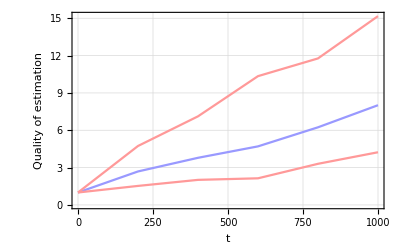

```mathematica
MeanQtyCdata=Transpose[{tpC,10^MeanQtyC}];
MeanQtyCData1=Transpose[{tpC,10^(MeanQtyC+DesvQtyC)}];
MeanQtyCData2=Transpose[{tpC,10^(MeanQtyC-DesvQtyC)}];
plot=ListPlot[{MeanQtyCdata,MeanQtyCData1,MeanQtyCData2},AxesLabel->{"t","|Err_Est|/|Err|"},Joined->True,
PlotRange->All,
PlotTheme->"Detailed",
PlotStyle->{StyleEstimation,Lighter[Red,.6],Lighter[Red,.6]},
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","Quality of estimation"}]
Export[NotebookDirectory[]<>ImagesDirectory<>"plot7b.pdf",Show[plot]];
```

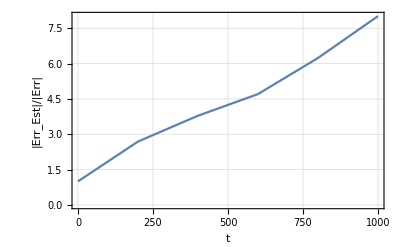

```mathematica
plot=ListPlot[{MeanQtyCdata},AxesLabel->{"t","|Err_Est|/|Err|"},Joined->True,
PlotRange->All,
PlotTheme->"Detailed",
BaseStyle->{FontSize->10,FontFamily->"Latin Modern Roman"},Frame->True,FrameLabel->{"t","|Err_Est|/|Err|"}]
```